## Information Relative Risk Aversion

## Derivation of IRRA

Relative Risk Aversion (RRA) of the Coupled Logarithm utility function

First replicate Wikipedia page on Relative Risk Aversion

```mathematica
RRA[c_,q_]:=-c D[qln[c,q],{c,2}]/D[qln[c,q],c];
qln[c_,q_]:=(c^(1-q)-1)/(1-q);
```

```mathematica
FullSimplify[RRA[c,q],1<q<3]
```

q

Review the Information Relative Risk from the perspective of utility to double check aversion/tolerance direction.  With straight line as utility function, risk averse has negative second derivative and risk tolerant has positive second derivative. For utility, use ln p rather than - ln p.

```mathematica
IRRA[p_,κ_,d_,α_]:=-p(D[-1/α CoupledLogarithm[p^-α,κ,d],{p,2}]/D[-1/α CoupledLogarithm[p^-α,κ,d],p]-D[Log[p^α],{p,2}]/D[Log[p^α],p]);
```

```mathematica
FullSimplify[{IRRA[p,κ,d,α],IRRA[p,κ,d,α]/.{κ->qToCoupling[q,α,d]}},κ>0&&α>0&&d>0&&0<p<1]
```

{(α κ)/(1+d κ),Piecewise[{{-1+q, (1-q)/(d-d q+α)≠0}, {0, True}}]}

Solve for Informational Relative Risk Aversion (IRRA) using the coupled surprisal in terms of the loss rather than the utility function.  The variable p is inverted to make it a loss function. The sign of the IRAA equation does not change because the sign of both the second and the first derivative changed. The ratio is unchanged.

```mathematica
IRRA[p_,κ_,d_,α_]:=-p(D[1/α CoupledLogarithm[p^-α,κ,d],{p,2}]/D[1/α CoupledLogarithm[p^-α,κ,d],p]-D[-Log[p^α],{p,2}]/D[-Log[p^α],p]);
```

```mathematica
FullSimplify[{IRRA[p,κ,d,α],IRRA[p,κ,d,α]/.{κ->qToCoupling[q,α,d]}},κ>0&&α>0&&d>0&&0<p<1]
```

{(α κ)/(1+d κ),Piecewise[{{-1+q, (1-q)/(d-d q+α)≠0}, {0, True}}]}

Thus it is the positive κ values that have positive values of IRAA.  The domain is - 0 <κ<∞.

Will use the expressions r = r_a=-r_tto label relative risk aversion and relative risk tolerance.

## Derivation of Decisive-Accuracy-Robustness Metric

From the Reduced Perplexity book chapter

Perhaps, I haven’t fully absorbed the significance of this equation.  The effect of weighting the generalized mean by the coupled probability is to change the sign of the generalized mean.  If I apply the generalized mean again, then the sign will reverse back.

However, the distinction with the assessment metric is that the equation is for the cross-entropy.  For p - empirical distribution and q - quoted forecast, the equation is

```mathematica
(∑_(i=1)^N (Subscript[p, i]^(1-r)/(∑_(j=1)^N Subscript[p, j]^(1-r)))Subscript[q, i]^r)^(1/r)=(1/(∑_(j=1)^N Subscript[p, j]^(1-r))∑_(i=1)^N Subscript[p, i](Subscript[q, i]/Subscript[p, i])^r)^(1/r)
```

Set::write: Tag Power in (∑_(i=1)^N (p_i^(1-r) q_i^r)/(∑_(j=1)^N p_j^(1«1»«5»«1»«1»])))^(1/r) is Protected.

((∑_(i=1)^N p_i (q_i/p_i)^r)/(∑_(j=1)^N p_j^(1-r)))^(1/r)

The derivation of the DAR metric should focus on use of the inverse coupled logarithm.
Given y=1/α CoupledLogarithm[p^-α,κ,d] as the coupled surprisal, the inverse of this to provide a probablity is (CoupledExponential[α y, κ, (d]))^(-1/α).

```mathematica
FullSimplify[( CoupledExponential[
FullSimplify[∑_(i=1)^N α/(α N)CoupledLogarithm[p^-α,κ,d],0<p<1&&0<α<∞&&0<κ<∞&&0<d<∞&&N∈Integers],
κ,d])^(-1/α),0<p<1&&0<α<∞&&0<κ<∞&&0<d<∞&&N∈Integers]
```

p

```mathematica
FullSimplify[( CoupledExponential[
FullSimplify[∑_(i=1)^n α/(α n)CoupledLogarithm[p[i]^-α,κ,d],0<p<1&&0<α<∞&&0<κ<∞&&0<d<∞&&N∈Integers],
κ,d])^(-1/α),0<p<1&&0<α<∞&&0<κ<∞&&0<d<∞&&N∈Integers]
```

If[1+κ ∑_(i=1)^n If[p[i]^-α≥0,If[κ≠0,((p[i]^-α)^(κ/(1+d κ))-1)/κ,Log[p[i]^-α]],Undefined]/n>0,If[κ≠0,(1+κ ∑_(i=1)^n If[p[i]^-α≥0,If[κ≠0,((p[i]^-α)^(κ/(1+d κ))-1)/κ,Log[p[i]^-α]],Undefined]/n)^((1+d κ)/κ),Exp[∑_(i=1)^n If[p[i]^-α≥0,If[κ≠0,((p[i]^-α)^(κ/(1+d κ))-1)/κ,Log[p[i]^-α]],Undefined]/n]],If[(1+d κ)/κ>0,0,∞]]^(-1/α)

```mathematica
FullSimplify[(1+κ ∑_(i=1)^n (((p[i]^-α)^(κ/(1+d κ))-1)/κ)/n)^((1+d κ)/(-α κ))]
```

(1+κ ∑_(i=1)^n (-1+(p[i]^-α)^(κ/(1+d κ)))/(n κ))^(-(1+d κ)/(α κ))

```mathematica
(1/n ∑_(i=1)^n (p[i]^((-α κ)/(1+d κ))))^(-(1+d κ)/(α κ))
```

So, indeed the RAD metric uses rt = (-α κ)/(1+d κ)as the metric; thus it is based on the relative risk tolerance.

## Plots of q-log and coupled log

Plot of the coupled logarithm as a utility function shows more negative curvature as κ is more positive.

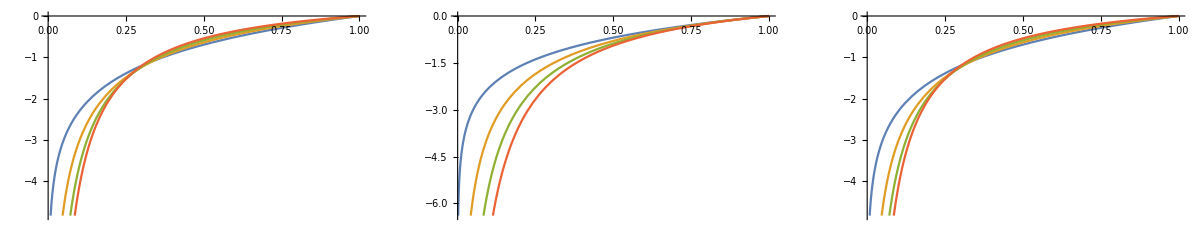

```mathematica
GraphicsGrid[{{Plot[Evaluate@(-1/α CoupledLogarithm[p^-α,#,d]&/@{0,0.25,.5,0.75}//.{α->2,d->1}),
{p,0,1}],
(* Not the exact same function *)
Plot[Evaluate@(qln[p,#]&/@couplingToq[{10^-6,0.25,.5,0.75},α,d]//.{α->2,d->1}),
{p,0,1}],
Plot[Evaluate@(1/α CoupledLogarithm[p^α,-#,-d]&/@{0,0.25,.5,0.75}//.{α->2,d->1}),
{p,0,1}]
}}]
```

Plot the coupled-surprisal as the information loss function

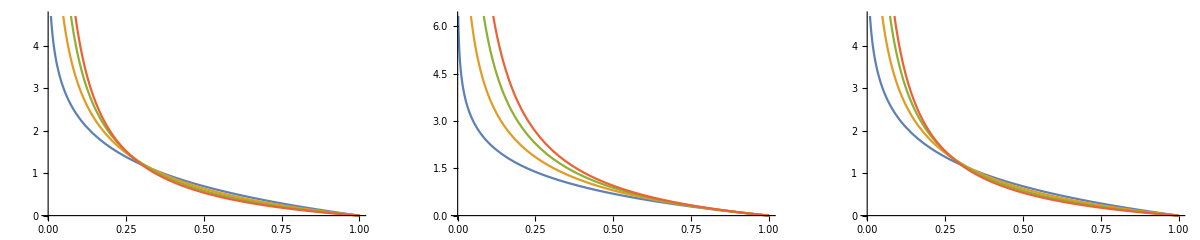

```mathematica
GraphicsGrid[{{Plot[Evaluate@(1/α CoupledLogarithm[p^-α,#,d]&/@{0,0.25,.5,0.75}//.{α->2,d->1}),
{p,0,1}],
Plot[Evaluate@(-qln[p,#]&/@couplingToq[{10^-6,0.25,.5,0.75},α,d]//.{α->2,d->1}),
{p,0,1}],
Plot[Evaluate@(-1/α CoupledLogarithm[p^α,-#,-d]&/@{0,0.25,.5,0.75}//.{α->2,d->1}),
{p,0,1}]
}}]
```

Curious what the curves look like if alpha = 1

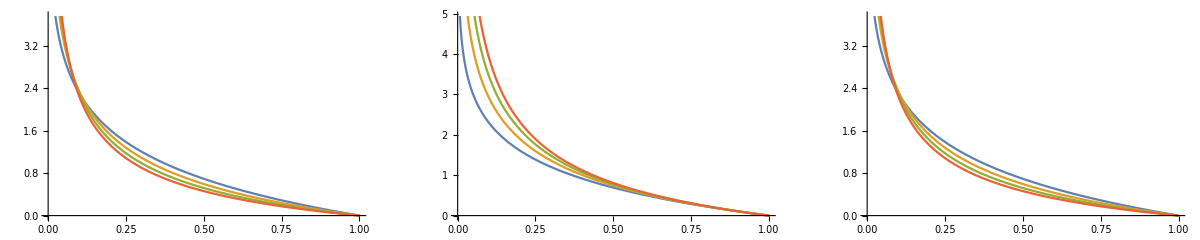

```mathematica
GraphicsGrid[{{Plot[Evaluate@(1/α CoupledLogarithm[p^-α,#,d]&/@{0,0.25,.5,0.75}//.{α->1,d->1}),
{p,0,1}],
Plot[Evaluate@(-qln[p,#]&/@couplingToq[{10^-6,0.25,.5,0.75},α,d]//.{α->1,d->1}),
{p,0,1}],
Plot[Evaluate@(-1/α CoupledLogarithm[p^α,-#,-d]&/@{0,0.25,.5,0.75}//.{α->1,d->1}),
{p,0,1}]
}}]
```